```mathematica
L = Sqrt[2];
h=1;
a = Pi/L; 
Pr=10;
Rl=30;
b=4*Pi^2/(a^2+Pi^2);
endTime=50;
coeff1=((a^2+Pi^2)*Sqrt[2])/(a*Pi);
solution=NDSolve[{
x'[t]==Pr*(y[t]-x[t]),
y'[t]==Rl*x[t]-x[t] z[t]-y[t],
z'[t]==x[t] y[t]-b* z[t],
x[0]==z[0]==1,
y[0]==0},
{x,y,z},
{t,0,endTime}];
Psi[wx_,wz_,t_]:=
(coeff1*x[t]/.solution)*Sin[Pi*wz]*Sin[a*wx];
```

```mathematica
ParametricPlot3D[
Evaluate[{x[t],y[t],z[t]}/.solution],
{t,0,50},
PlotPoints->5000
]
```

-Graphics3D-

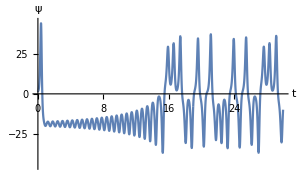

```mathematica
Plot[
Psi[L/2,3/4,s],
{s,0,30},
PlotPoints->600,
PlotRange->{-45,45},
AxesLabel->{"t","ψ"}]
```